# The Collatz Conjecture

## One of the most famous unsolved problems in mathematics

## Definition

The Collatz Conjecture states that repetition of a simple rule on any positive integer will eventually converge to 1. The rule is: if the number is even, divide by 2; if the number is odd, multiple by three and add 1. 

Let's implement the function in the Wolfram Language, allowing the function to memorize it as it is called:

```mathematica
Collatz[1]:=1;
Collatz[n_?EvenQ]:=Collatz[n]=Collatz[n/2]
Collatz[n_?OddQ]:=Collatz[n]=Collatz[3n+1]
```

When called, the function will recursively evaluate until hitting 1.

Let's test it for arbitrarily large numbers:

```mathematica
Collatz/@{5,222,9123,100001}
```

{1,1,1,1}

Now, test it for all numbers up to a certain limit:

```mathematica
DeleteDuplicates[Collatz/@Range[5000000]]
```

{1}

This doesn't prove the conjecture, but it does verify it for small numbers.

## Visualization:

To explore the patterns of convergence, it is useful to define a new function, which lists the path every number takes to get to 1.

```mathematica
CollatzList[1]:=1;
CollatzList[n_ /;EvenQ[n]]:=CollatzList[n]=Flatten[{n,CollatzList[n/2]}];
CollatzList[n_/; OddQ[n]]:=CollatzList[n]=Flatten[{n,CollatzList[3n+1]}];
```

Start by visualizing how often the paths pass through each number.

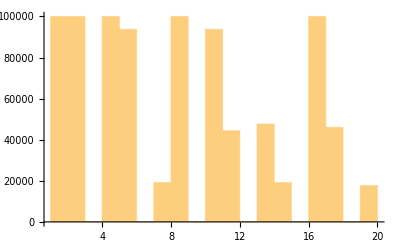

```mathematica
Histogram[Flatten[Map[CollatzList,Range[100000]]],{1,20,1}]
```

The frequency on this chart is the number of integers from 1 to 100,000 that pass through the specified number before converging to 1. Every path must eventually pass through a power of two before reaching 1; this is illustrated by the histogram peaks at these numbers. The histogram nearly vanishes at every multiple of 3, indicating very few paths pass through these numbers. The distribution at the remaining integers seems more random.

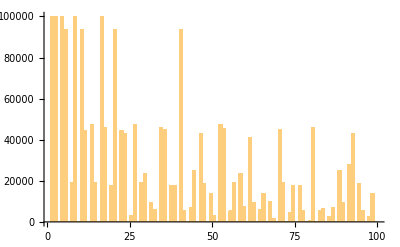

```mathematica
Histogram[Flatten[Map[CollatzList,Range[100000]]],{1,100,1}]
```

Over a wider range, the random pattern seems to continue.

Now, view the number of steps required by each integer to reach 1. First, convert the list of paths into a list of steps.

```mathematica
RuleList[n_]:=Thread[Partition[CollatzList[n],2,1][[All,1]]-> Partition[CollatzList[n],2,1][[All,2]]];
```

The length of the list of steps gives the length of the path from every integer to 1.

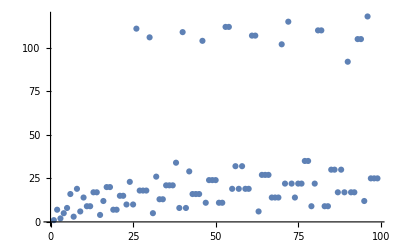

```mathematica
ListPlot[Table[Length[RuleList[n]],{n,Range[2,100]}],PlotRange->All]
```

At low integer values, the path lengths seem to scale like Sqrt[n], with a set of exceptions above the main group.

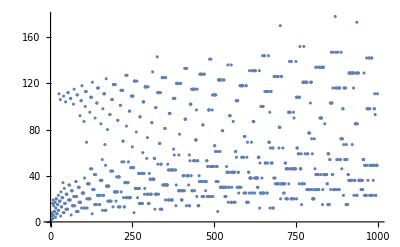

```mathematica
ListPlot[Table[Length[RuleList[n]],{n,Range[2,1000]}],PlotRange->All]
```

With a larger set of integers, the previous exceptions look like a wholly separate pattern, characterized by longer paths.

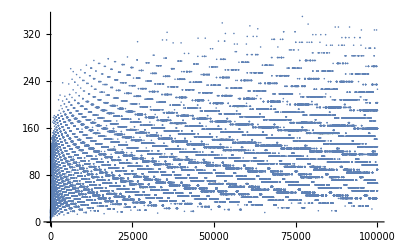

```mathematica
ListPlot[Table[Length[RuleList[n]],{n,Range[2,100000]}],PlotRange->All]
```

As n gets very large, the lengths of the paths clearly follow a complex pattern, yet one that has a high degree of nesting.

To further investigate the chaotic nature of the Conjecture, the data can be interpreted as a graph. To do so, the list of rules for each integer must be turned into a total list of edges.

```mathematica
Nmax=24;totalRuleList=DeleteDuplicates[Flatten[Table[RuleList[n],{n,2,Nmax,1}]]];
```

Now, these edges can be used to construct a graph. To make reading it easier, 1 has been marked in red.

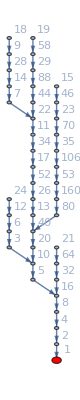

```mathematica
Graph[totalRuleList,GraphLayout->"LayeredDigraphEmbedding",VertexStyle->{1 -> Red},VertexSize->{1-> Large},VertexLabels->"Name"]
```

For a sequence to converge, it must eventually hit the main "backbone" of the graph, consisting of powers of 2. The largest power of two can be calculated from the list of rules.

```mathematica
maxPower2=Max[Select[Log[2,#]&/@totalRuleList[[All,1]],IntegerQ]];
```

This can be used to highlight this "backbone."

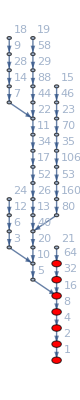

```mathematica
Graph[totalRuleList,GraphLayout->"LayeredDigraphEmbedding",VertexStyle->Table[2^n-> Red,{n,0,maxPower2}],VertexSize->Table[2^n-> Large,{n,0,maxPower2}],VertexLabels->"Name"]
```

More complex graphs emerge as the number of nodes grows. By repeating the same commands, the graph can be made bigger. For clarity, numerical labels are omitted.

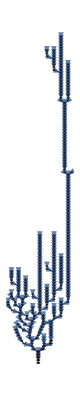

```mathematica
Nmax=128;
totalRuleList=DeleteDuplicates[Flatten[Table[RuleList[n],{n,2,Nmax,1}]]];
maxPower2=Max[Select[Log[2,#]&/@totalRuleList[[All,1]],IntegerQ]];
Graph[totalRuleList,GraphLayout->"LayeredDigraphEmbedding",VertexStyle->Table[2^n-> Red,{n,0,maxPower2}],VertexSize->Table[2^n-> Large,{n,0,maxPower2}]]
```

The tree-like structure of the Collatz Conjecture becomes more apparent. Once more the number of nodes is increased. For clarity, the vertices are hidden.

```mathematica
Nmax=256;
totalRuleList=DeleteDuplicates[Flatten[Table[RuleList[n],{n,2,Nmax,1}]]];
maxPower2=Max[Select[Log[2,#]&/@totalRuleList[[All,1]],IntegerQ]];
Graph[totalRuleList,GraphLayout->"LayeredDigraphEmbedding",VertexSize->0]
```

-Graphics-

Clearly, the rules associated with the Collatz Conjecture generate a highly complex, and seemingly random structure.

#### Further Explorations

Goldbach's conjecture

Brocard's problem

#### Authorship information

Marc Thomson

June 21, 2017

marc.thomson@colorado.edu